## Exercise 1: survival -- fecundity trade-off

```mathematica
Clear["Global`*"];
```

### Invasion fitness of mutant

```mathematica
w=smax y+(1-smax x)f[y]/f[x]
```

smax y+((1-smax x) f[y])/f[x]

```mathematica
S = D[w,y] /.y->x
```

smax+((1-smax x) f'[x])/f[x]

```mathematica
S /. f-> Function[z,fmax (1-z^2)] //FullSimplify
Solve[% == 0,x]
```

(smax-2 x+smax x^2)/(1-x^2)

{{x→(1-√(1-smax^2))/smax},{x→(1+√(1-smax^2))/smax}}

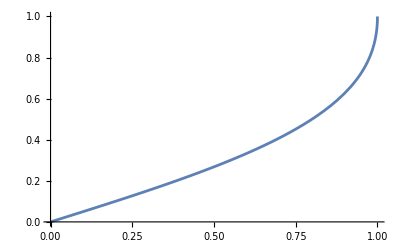

```mathematica
Plot[(1-√(1-smax^2))/smax,{smax,0,1}]
```

```mathematica
J=D[S,x];
J/. f-> Function[z,fmax (1-z^2)] //FullSimplify  ;
% /.x->  (1-√(1-smax^2))/smax //FullSimplify
```

-1-√(1-smax^2)

```mathematica
H  = D[w,y,y] /.y->x ;
H /. f-> Function[z,fmax (1-z^2)] //FullSimplify  ;
% /.x->  (1-√(1-smax^2))/smax //FullSimplify
```

-1-√(1-smax^2)

### General branching condition

```mathematica
Solve[S == 0,f'[x]]
```

{{f'[x]→(smax f[x])/(-1+smax x)}}

```mathematica
D[w,y,x] /.y->x /. f'[x]->(smax f[x])/(-1+smax x) //Simplify
```

0

Hence branching is impossible.

```mathematica
J /. f'[x]->(smax f[x])/(-1+smax x)  //FullSimplify 
H /. f'[x]->(smax f[x])/(-1+smax x)  //FullSimplify
```

((1-smax x) f''[x])/f[x]

((1-smax x) f''[x])/f[x]

## Exercise 2: the evolution of aggressivity

### Expected payoff of a mutant y in a resident pop x

```mathematica
Clear["Global`*"];
```

```mathematica
Payoff = y x (v/2-c)+ y (1-x)v + (1-y)x *0 + (1-y)(1-x)v/2 ;
```

```mathematica
(* resident payoff *)
PayoffRes =  Payoff /. y-> x ;
```

```mathematica
w= (1+δ Payoff)/(1+δ PayoffRes)  ;
w = Normal[Series[w,{δ,0,1}]] ;
w =w /.δ->1
```

1+1/2 (-v x+2 c x^2+v y-2 c x y)

```mathematica
S = D[w,y] /.y->x //Simplify
```

1/2 (v-2 c x)

```mathematica
equi = Flatten@Solve[S == 0,x]
```

{x→v/(2 c)}

```mathematica
J=D[S,x]/.   equi //Simplify
```

-c

```mathematica
Reduce[J< 0&& v> 0&&c> 0]
```

v>0&&c>0

```mathematica
H  = D[w,y,y] /.y->x /.   equi //Simplify
```

0

### With cost to flexibility

```mathematica
Clear["Global`*"];
```

```mathematica
Payoff = y x (v/2-c)+ y (1-x)v + (1-y)x *0 + (1-y)(1-x)v/2  -cf  y(1-y) ;
```

```mathematica
(* resident payoff *)
PayoffRes =  Payoff /. y-> x ;
```

```mathematica
w= (1+δ Payoff)/(1+δ PayoffRes)  ;
w = Normal[Series[w,{δ,0,1}]] ;
w =w/. δ->1
```

1+1/2 (2 cf x-v x+2 c x^2-2 cf x^2-2 cf y+v y-2 c x y+2 cf y^2)

```mathematica
S = D[w,y] /.y->x //Simplify
```

1/2 (v-2 c x+cf (-2+4 x))

```mathematica
equi = Flatten@Solve[S == 0,x]
```

{x→(-2 cf+v)/(2 (c-2 cf))}

```mathematica
J=D[S,x]/.   equi //Simplify
```

-c+2 cf

```mathematica
H  = D[w,y,y] /.y->x /.   equi //Simplify
```

2 cf

```mathematica
Reduce[J< 0&& H> 0&& v> 0&&c> 0 && cf>0 && 0<(-2 cf+v)/(2 (c-2 cf))<1]
```

v>0&&0<cf<v/2&&c>1/2 (2 cf+v)